```mathematica
f=(1/Sqrt[Pi])*(2/a0)^(3/2)*Exp[-2r1/a0]*(1/Sqrt[Pi])*(2/a0)^(3/2)*Exp[-2r2/a0]
```

(8 ⅇ^(-(2 r1)/a0-(2 r2)/a0))/(a0^3 π)

```mathematica
e^2*Integrate[f^2*1/Sqrt[r1^2+r2^2-2r1*r2*Cos[t2]]*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi}]
```

ConditionalExpression[(5 e^2)/(4 a0), Re[a0]>0]

```mathematica
g=(1/Sqrt[Pi])*(Z/a0)^(3/2)*Exp[-Z*r1/a0]*(1/Sqrt[Pi])*(Z/a0)^(3/2)*Exp[-Z*r2/a0]
```

(ⅇ^(-(r1 Z)/a0-(r2 Z)/a0) Z^3)/(a0^3 π)

```mathematica
first=
```

```mathematica
e^2*Integrate[g^2*(Z-2)/r1*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{Z/a0>0}]
```

(e^2 (-2+Z) Z)/a0

```mathematica
third=e^2*Integrate[g^2*1/Sqrt[r1^2+r2^2-2r1*r2*Cos[t2]]*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{Z/a0>0}]
```

(5 e^2 Z)/(8 a0)

```mathematica
h[Z_]:=-Z^2+(5 Z)/8+2Z(Z-2);
```

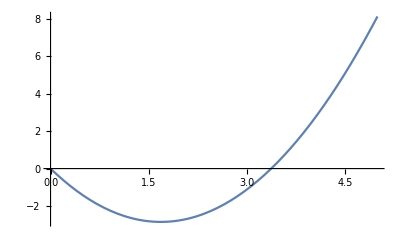

```mathematica
Plot[h[z],{z,0,5}]
```

```mathematica
Solve[D[h[z],z]==0,z]
```

{{z→27/16}}

```mathematica
h[27/16]
```

-729/256

```mathematica
N[27/16]
```

1.6875

```mathematica
(*Bonus*)
```

```mathematica
ψ[r1_,r2_,t2_]:=(1+c2*Sqrt[r1^2+r2^2-2r1*r2*Cos[t2]]+c3*(r1-r2)^2)*E^(-c1*(r1+r2));
```

```mathematica
Sqrd=ψ[r1,r2,t2]^2//FullSimplify
```

ⅇ^(-2 c1 (r1+r2)) (1+c3 (r1-r2)^2+c2 √(r1^2+r2^2-2 r1 r2 Cos[t2]))^2

```mathematica
Integrate[Sqrd*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{c1->Reals,c2->Reals,c3->Reals}]
```

ConditionalExpression[((8 c1^4+35 c1^3 c2+77 c1 c2 c3+72 c3^2+24 c1^2 (2 c2^2+c3)) π^2)/(8 c1^10), Re[c1]>0]

```mathematica
Integrate[(1/r1)*Sqrd*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{c1->Reals,c2->Reals,c3->Reals}]
```

ConditionalExpression[((4 c1^4+15 c1^3 c2+35 c1 c2 c3+36 c3^2+6 c1^2 (3 c2^2+2 c3)) π^2)/(4 c1^9), Re[c1]>0]

```mathematica
Integrate[(-1/2)*D[r1^2*D[ψ[r1,r2,t2],r1],r1]*ψ[r1,r2,t2]*r2^2*Sin[t2]*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{c1->Reals,c2->Reals,c3->Reals}]
```

-4 π^2 Integrate[r1 r2^2 Sin[t2] ψ[r1,r2,t2] (2 ψ^(1,0,0)[r1,r2,t2]+r1 ψ^(2,0,0)[r1,r2,t2]),{r1,0,∞},{r2,0,∞},{t2,0,π},Assumptions→{c1→ℝ,c2→ℝ,c3→ℝ}]

```mathematica
Solve[w2(1+vR/c)==w1(1-vR/c),vR]
```

{{vR→(c (w1-w2))/(w1+w2)}}

```mathematica
(*****************************************************************)
```

```mathematica
Integrate[(1/Sqrt[Pi])^2((1/a0)^(3/2)*Exp[-r/a0])^2*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{p,0,2Pi}]
```

ConditionalExpression[1, Re[a0]>0]

```mathematica
psi100=(1/Sqrt[Pi])*(1/a0)^(3/2)*Exp[-r/a0];
```

```mathematica
Integrate[psi100*psi100*(e^2/r-(e^2/(2*rp))*(3-r^2/rp^2))*r^2*Sin[t],{r,0,rp},{t,0,Pi},{p,0,2Pi}]//FullSimplify
```

(e^2 (3 a0^3-3 a0 rp^2+2 rp^3-3 a0 ⅇ^(-(2 rp)/a0) (a0+rp)^2))/(2 a0 rp^3)

```mathematica
Integrate[r^2*2*e^2/(r0*a^3)*((r/r0)^2-3+2r0/r)*Exp[-2r/a],{r,0,r0}]
```

(e^2 (3 a^3-3 a r0^2+2 r0^3-3 a ⅇ^(-(2 r0)/a) (a+r0)^2))/(2 a r0^3)

```mathematica
FullSimplify[Series[Exp[-x],{x,0,6}]]/.{x->2*rp/a0}
```

SeriesData::sdatv: First argument (2 rp)/a0 is not a valid variable.

1-(2 rp)/a0+1/2 ((2 rp)/a0)^2-1/6 ((2 rp)/a0)^3+1/24 ((2 rp)/a0)^4-1/120 ((2 rp)/a0)^5+1/720 ((2 rp)/a0)^6+O[(2 rp)/a0]^7

```mathematica
1/(2 a0 rp^3)e^2 (3 a0^3-3 a0 rp^2+2 rp^3-3 a0(1-(2 rp)/a0+1/2 ((2 rp)/a0)^2-1/6 ((2 rp)/a0)^3+1/24 ((2 rp)/a0)^4-1/120 ((2 rp)/a0)^5+1/720 ((2 rp)/a0)^6) (a0+rp)^2)//Expand
```

(2 e^2 rp^2)/(5 a0^3)-(e^2 rp^3)/(3 a0^4)+(2 e^2 rp^4)/(15 a0^5)-(2 e^2 rp^5)/(15 a0^6)

```mathematica
(1/(Pi*a0^3))*Integrate[Exp[-2r/a0]*(e^2/r-(e^2/(2rp))*(3-r^2/rp^2))*r^2*Sin[t],{r,0,rp},{t,0,Pi},{p,0,2Pi}]
```

(e^2 (3 a0^3-3 a0 rp^2+2 rp^3-3 a0 ⅇ^(-(2 rp)/a0) (a0+rp)^2))/(2 a0 rp^3)

```mathematica
(4/5)*13.6*(0.9*10^(-15)/(5.291*10^(-11)))^2
```

3.14803×10^-9

```mathematica
3.1480265840500202*^-9*(1.602*(10^(-19)))
```

5.04314×10^-28

```mathematica
5.0431385876481325*^-28/(6.626*10^(-34))
```

761114.

```mathematica
761113.5809912664/(2*Pi)
```

121135.

```mathematica
psi200=(1/4)*(1/Sqrt[2*Pi])*(1/a0)^(3/2)*Exp[-r/(2*a0)]*(2-r/a0);
```

```mathematica
Integrate[psi200^2*r^2*Sin[t],{r,0,Infinity},{t,0,Pi},{p,0,2Pi}]
```

ConditionalExpression[1, Re[a0]>0]

```mathematica
Integrate[psi200^2*(e^2/r-(e^2/(2*rp))*(3-r^2/rp^2))*r^2*Sin[t],{r,0,rp},{t,0,Pi},{p,0,2Pi}]
```

(e^2 (336 a0^7-24 a0^5 rp^2+4 a0^4 rp^3-6 a0^3 ⅇ^(-rp/a0) (56 a0^4+56 a0^3 rp+24 a0^2 rp^2+6 a0 rp^3+rp^4)))/(16 a0^5 rp^3)

```mathematica
(e^2 (336 a0^7-24 a0^5 rp^2+4 a0^4 rp^3-6 a0^3 ⅇ^(-rp/a0) (56 a0^4+56 a0^3 rp+24 a0^2 rp^2+6 a0 rp^3+rp^4)))/(16 a0^5 rp^3)//TeXForm
```

\frac{e^2 \left(336 \text{a0}^7-24 \text{a0}^5 \text{rp}^2+4 \text{a0}^4 \text{rp}^3-6
   \text{a0}^3 e^{-\frac{\text{rp}}{\text{a0}}} \left(56 \text{a0}^4+56 \text{a0}^3
   \text{rp}+24 \text{a0}^2 \text{rp}^2+6 \text{a0}
   \text{rp}^3+\text{rp}^4\right)\right)}{16 \text{a0}^5 \text{rp}^3}

```mathematica
FullSimplify[Series[Exp[-x],{x,0,6}]]/.{x->rp/a0}
```

SeriesData::sdatv: First argument rp/a0 is not a valid variable.

1-rp/a0+1/2 (rp/a0)^2-1/6 (rp/a0)^3+1/24 (rp/a0)^4-1/120 (rp/a0)^5+1/720 (rp/a0)^6+O[rp/a0]^7

```mathematica
1/(16 a0^5 rp^3)e^2 (336 a0^7-24 a0^5 rp^2+4 a0^4 rp^3-6 a0^3 (1-rp/a0+1/2 (rp/a0)^2-1/6 (rp/a0)^3+1/24 (rp/a0)^4-1/120 (rp/a0)^5+1/720 (rp/a0)^6)(56 a0^4+56 a0^3 rp+24 a0^2 rp^2+6 a0 rp^3+rp^4))//Expand
```

(e^2 rp^2)/(20 a0^3)-(e^2 rp^3)/(24 a0^4)+(7 e^2 rp^4)/(480 a0^5)-(3 e^2 rp^5)/(320 a0^6)-(e^2 rp^7)/(1920 a0^8)

```mathematica
6.626*3*1.09678
```

21.8018

```mathematica
(3/4)*13.6*(1.602*10^(-19))/(6.626*10^(-34))
```

2.4661×10^15

```mathematica
2/5-1/20
```

7/20

```mathematica
2(7/20)*13.6*(0.9*10^(-15)/(5.291*10^(-11)))^2*(1.602*(10^(-19)))/(6.626*10^(-34))
```

665974.

```mathematica
2(7/20)*13.6*(0.91*10^(-15)/(5.291*10^(-11)))^2*(1.602*(10^(-19)))/(6.626*10^(-34))
```

680856.

```mathematica
2(7/20)*13.6*(0.89*10^(-15)/(5.291*10^(-11)))^2*(1.602*(10^(-19)))/(6.626*10^(-34))
```

651257.

```mathematica
(0.01*10^-15)^2*Sqrt[2]*(7/20)*(13.6*2)*(1/(5.291*10^(-11)))^2(1.602*(10^(-19)))/(6.626*10^(-34))
```

116.275